# Mathematica bugs

## Problems with function “Show”

## Problems with showing BarChart

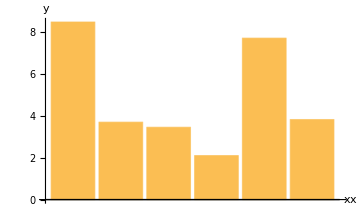

```mathematica
BarChart[Table[RandomReal[10],6],ImageSize->Medium,AxesLabel->{"x","y"}]
```

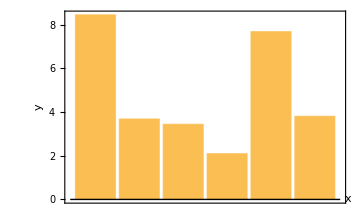

```mathematica
Show[%,Frame->True,
Axes->False,AxesLabel->None,
LabelStyle->{FontFamily->"Helvetica",FontSize->15,FontWeight->Bold,FontColor->Black},
FrameTicks->{{Automatic,None},{None,None}},
FrameLabel->{None,"y"}]
```

x axes is till there, which is ugly.

## SetOption not working for DateListPlot

```mathematica
data=Table[{Today+Quantity[i,"Days"],i},{i,10}]
```

{{Day: Sat 21 Sep 2019,1},{Day: Sun 22 Sep 2019,2},{Day: Mon 23 Sep 2019,3},{Day: Tue 24 Sep 2019,4},{Day: Wed 25 Sep 2019,5},{Day: Thu 26 Sep 2019,6},{Day: Fri 27 Sep 2019,7},{Day: Sat 28 Sep 2019,8},{Day: Sun 29 Sep 2019,9},{Day: Mon 30 Sep 2019,10}}

```mathematica
SetOptions[DateListPlot,Mesh->Full,ImageSize->Large,GridLines->Automatic,LabelStyle->{FontFamily->"Helvetica",FontSize->14,FontWeight->Bold,FontColor->Black}];
```

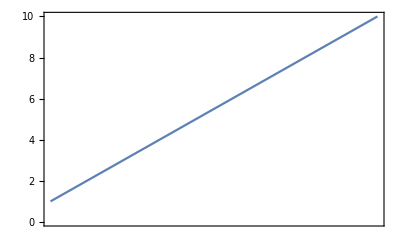

```mathematica
DateListPlot@data
```

```mathematica
SetOptions[ListPlot,ImageSize->Large,Frame->{{True,True},{True,True}},FrameStyle->Directive[Black,Thickness[0.003]],FrameTicks->{{Automatic,None},{Automatic,None}},GridLines->Automatic,LabelStyle->{FontFamily->"Helvetica",FontSize->18,FontWeight->Bold,FontColor->Black},ImageMargins->15];
```

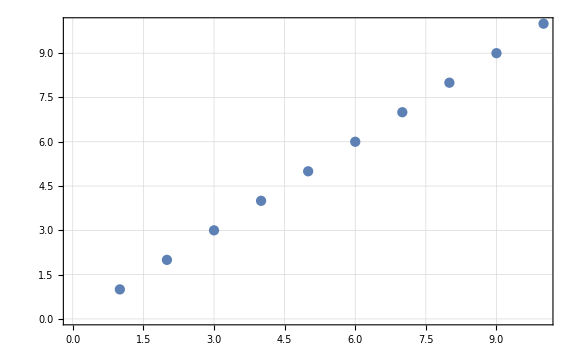

```mathematica
ListPlot[Last/@data]
```

## Problem with TimeSeries

## Unrecognized timezone

```mathematica
$TimeZone=Entity["TimeZone","America/Phoenix"];
```

```mathematica
data={{DateObject[{2015,4,1,5,48,0.},"Instant","Gregorian","America/Phoenix"],6.},{DateObject[{2015,4,1,5,49,0.},"Instant","Gregorian","America/Phoenix"],7.},{DateObject[{2015,4,1,5,50,0.},"Instant","Gregorian","America/Phoenix"],8.}};
```

```mathematica
TimeSeries@data
```